```mathematica
p = PoissonDistribution[λ]
Mean[p]
Expectation[x^2, Distributed[x, p]]
Expectation[(x+2)(x+1), Distributed[x, p]]
```

PoissonDistribution[λ]

λ

λ+λ^2

2+4 λ+λ^2

```mathematica
distx = NormalDistribution[0, 1]
disty = NormalDistribution[0, 1]
Expectation[1/y^2, y\[Distributed]disty ]
Expectation[x^2/y^2,{x \[Distributed]distx, y\[Distributed]disty}]
```

NormalDistribution[0,1]

NormalDistribution[0,1]

Expectation[1/y^2,y\[Distributed]NormalDistribution[0,1]]

-1

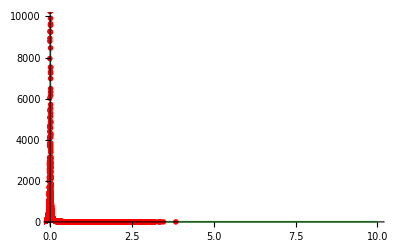

```mathematica
data=RandomVariate[NormalDistribution[0,1],10000];
filteredData=Select[data,#≠0&];
Plot[1/x^2,{x,0.01,10},Filling->Axis,PlotRange->All,PlotStyle->Directive[Green,Opacity[0.5]],Epilog->{Red,PointSize[0.01],Point[{#,1/#^2}&/@filteredData]}]
```